# px5503 - Data Visualisation 7 - Aesthetics and layout

## Aesthetics

We should strive to make our data visualisations pleasing to the eye. People respond better to aesthetically pleasing graphs, and are more likely to believe our message. Aesthetics is a complicated subject, which cannot be completely reduced to a set of well-defined rules. There are, however, some guidelines that will improve the aesthetic appeal of our plots.

### No clutter

We have introduced in a previous section the idea that a plot should be clean, that is, without spurious features that do not contribute to communicating the main message. The reason we gave was that useless extra features in a plot take attention away from the main message. But in addition to that, cleaner plots are almost always perceived as better looking. Extra stuff in the plot that is doing nothing makes plots feel messy, amateurish.

### Regularity and order

Orderly charts, where the elements follow a regular arrangement, look better than charts where things are placed randomly, with no rhyme or reason.

One of the most important manifestations of this principle is that elements in a plot should be aligned as much as possible along horizontal or vertical lines. For example, if we examine this plot:

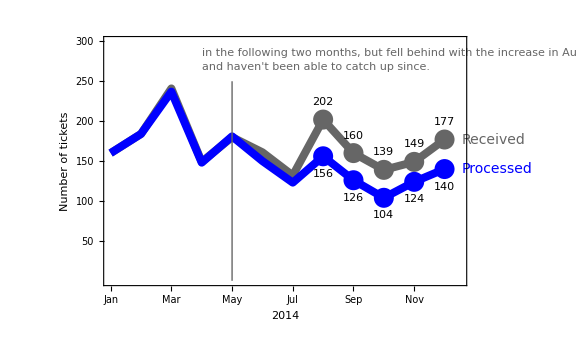

Notice how the vertical axis labels are aligned to the right, and the horizontal ones are aligned horizontally; the vertical tick marks are also aligned vertically. The title is aligned to the whole plot. The two labels “Received” and “Processed” are left-aligned, as are the lines of the inset text. All of this contributes to a general feeling of orderliness, despite the fact that the data itself is quite “messy”. Compare this with a version of this plot where we neglect alignment:

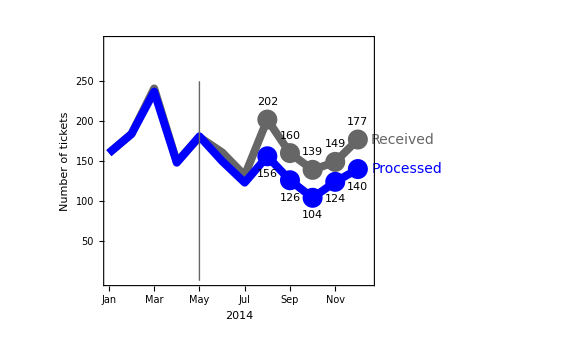

The lack of alignment makes this look a lot worse than the original version.

Alignment is not the only aspect of positioning of plot elements that affects the aesthetics. Regular spacing is also important. For example, we expect the axes tick labels and tick marks to be regularly spaced along their axes; and the same is true for the spacing between lines in multi-line text. If that is not respected, the plot looks messy, hurried, and unfinished:

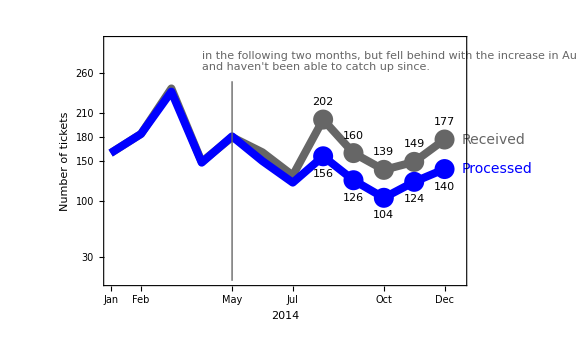

A less obvious place where regular spacing is also important is on the data labels for August and later. Even though the data itself is of course not aligned, it is important to make the spacing between each data point and its label the same throughout. If you don’t do that, we get a very messy result:

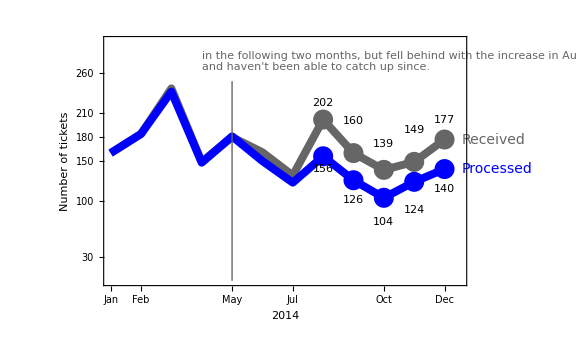

In addition to regularity in the spacing, regularity in other features is also important. For example:

The change in fonts and styles on the vertical axis is jarring. We expect ticks and tick labels on axes to be displayed in the same way, unless there is a good reason for it.

### Prefer horizontal and vertical features to diagonal ones

In Plots, we tend to find horizontal and vertical features and alignment to diagonal ones. Consider this example:

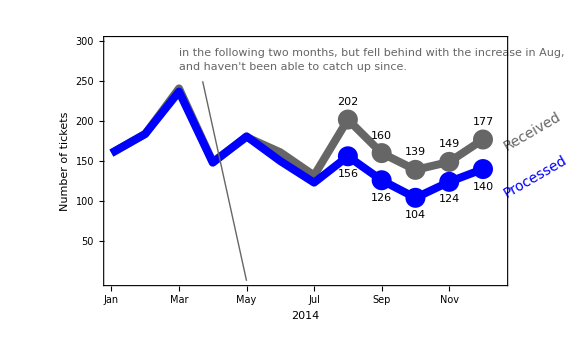

The diagonal line from May to the text and the tilted “received” and “processed” labels make this plot look noticeably worse than the original version. As much as possible, keep things aligned horizontally and vertically in your plots; avoid diagonals.

### Economy

Plot elements that play more than one role enhance that plot’s aesthetics. For example:

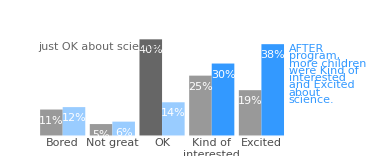

Here the “BEFORE” and “AFTER” labels tell the story, and highlight the plot’s point. But in addition to that, they also play the role that in other plots is played by legends - they tell us that gray colours mean “before”, and blue colours mean “after”. This is a clever use of inset text to multiple purposes. It negates the need for a separate legend, uncluttering the plot, and it makes it look better.

## Layout

We already discussed issues of layout related to aesthetics - most elements of a plot should be aligned horizontally or vertically, and repeated features such as axis ticks and tick labels should be spaced regularly. Here we will discuss how layout relates to highlighting.

When we see an image, our eyes tend to scan that image following the zigzag pattern depicted below:

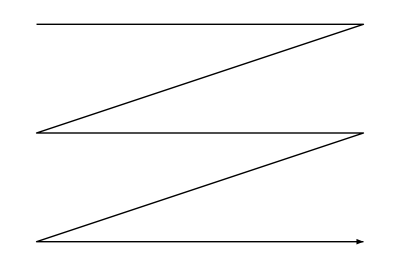

In other words, we  tend to scan an image as if it were a comic book, from top left to top right, going down towards the bottom. Most of us have an inbuilt ranking of the corners of a page or an image: from top to bottom, and from left to right.

When it comes to graphs, this means that the title is the very first thing we are likely to focus on. So the title should encapsulate our take-home message, whenever possible. We also should reinforce its focus by using large fonts and intense shades. Here is an example:

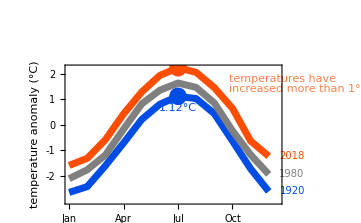

The title shouts the message loud and clear, and that message is then reinforced by every feature in the plot. Contrast this with this other version:

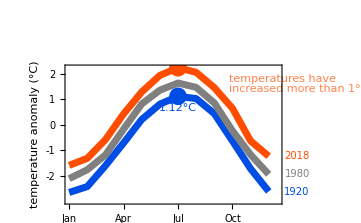

Now the title is just an inane restatement of things that are already well explained in the rest of the plot: the label for the vertical axis makes it clear that this is a plot of temperatures, and this is explained further by the sub-title; and the labels for each curve, showing the year it refers to, makes it clear this is a plot of a few “selected years”. This title is simply redundant; it adds nothing at all to the plot. Titles like this just waste one of the most prominent spots in a graph - its title - with inanities. Use your titles to say something important!

### Subtitles

Subtitles can be used to add information about the plot in a non-intrusive way. In this example:

The subtitle is used here to explain what is being plotted - in this case, what the quantity “temperature anomaly” means. Another example is this:

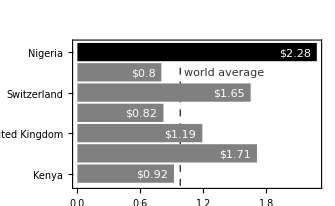

```mathematica
countries = {"Kenya", "Japan", "United Kingdom", "United States", 
			 "Switzerland", "Germany", Style["Nigeria",Black]};
priceOfMilk = {0.92, 1.71, 1.19, 0.82, 1.65, 0.80, Style[2.28,Black]};
avgPrice = 0.98;

BarChart[priceOfMilk,
	ChartLabels->Map[Style[#, RGBColor[0.5,0.5,0.5,1]]&, countries],
	BarOrigin->Left,
	Frame->True,
	LabelingFunction->(Placed[Style[Row[{"$", #}], White],
	                          Right]&),
	PlotLabel->Style["\n", 20],
	FrameStyle->RGBColor[1,1,1,0],
	ChartStyle->Directive[GrayLevel[0.5], EdgeForm[None]],
	PlotRangeClipping->False,
	
	Prolog->{
		GrayLevel[0.2], 
		Text["world average", {1.02,6}, {-1,0}],
		Dashed,
		Line[{{avgPrice,0.4}, {avgPrice,7.3}}],
		
		Style[Text["Milk is too expensive in Nigeria!",
		           {-0.65,8.7}, {-1,-1}],
		      FontSize->16, GrayLevel[0.3]],
		Style[Text["Price of 1 litre of milk in US dollars",
		           {-0.65,8}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]]		      
	}
]
```

Here we explain what the bars mean in the subtitle. This is better than placing this information on the default location at the bottom of the plot, where the x axis is traditionally drawn:

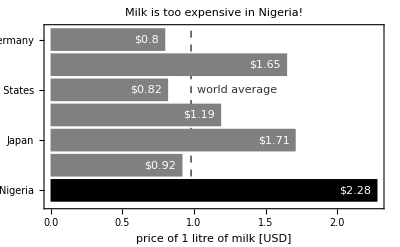

To begin with, this version is just plain uglier than the former one, because of the excessive white space at the bottom and the lack of alignment of the title and the x axis. In addition to that, in the former version the explanation of what the numbers mean is right at the top of the plot, next to the title; so most people will read that before they proceed to look at the rest of the plot, and will understand what the bars mean right away. In the version above, that information is only found at the bottom, and the viewer will have to do some backtrack in order to figure out the plot.

We can improve this plot further, by placing Nigeria at the very top. In most bar charts, the order of the bars has no intrinsic meaning, and we can shuffle them around to suit our needs. This takes advantage of the principle that features at the top are more prominent than those near the bottom.

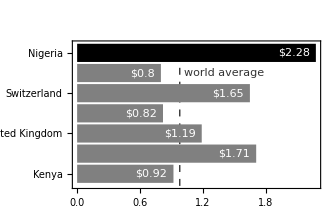

```mathematica
countries = {"Kenya", "Japan", "United Kingdom", "United States", 
			 "Switzerland", "Germany", Style["Nigeria",Black]};
priceOfMilk = {0.92, 1.71, 1.19, 0.82, 1.65, 0.80, Style[2.28,Black]};
avgPrice = 0.98;

BarChart[priceOfMilk,
	ChartLabels->Map[Style[#, RGBColor[0.5,0.5,0.5,1]]&, countries],
	BarOrigin->Left,
	Frame->True,
	LabelingFunction->(Placed[Style[Row[{"$", #}], White],
	                          Right]&),
	PlotLabel->Style["\n", 20],
	FrameStyle->RGBColor[1,1,1,0],
	ChartStyle->Directive[GrayLevel[0.5], EdgeForm[None]],
	PlotRangeClipping->False,
	
	Prolog->{
		GrayLevel[0.2], 
		Text["world average", {1.02,6}, {-1,0}],
		Dashed,
		Line[{{avgPrice,0.4}, {avgPrice,7.3}}],
		
		Style[Text["Milk is too expensive in Nigeria!",
		           {-0.65,8.7}, {-1,-1}],
		      FontSize->16, GrayLevel[0.3]],
		Style[Text["Price of 1 litre of milk in US dollars",
		           {-0.65,8}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]]		      
	}
]
```

We also place the “world average” annotation right next to the Nigeria bar, because comparing the average to the price in Nigeria is the main reason the average is in the plot.

We can improve make this plot one more time, by using the aesthetic principle of regularity. Our minds just like regularity over chaos, and any rearrangement of a chart that increases regularity will usually make it look better. Since the order of the bars in this plot is arbitrary and up to us, we can order the bars by their lengths:

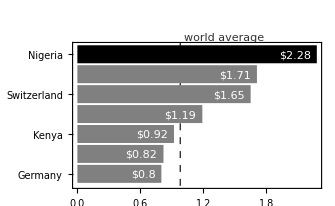

```mathematica
countriesM = {"Kenya", "Japan", "United Kingdom", "United States", 
			 "Switzerland", "Germany", Style["Nigeria",Black]};
priceOfMilkM = {0.92, 1.71, 1.19, 0.82, 1.65, 0.80, Style[2.28,Black]};
pts = Transpose[{countriesM,priceOfMilkM}];
orderedPts = SortBy[pts, #⟦2⟧&];
{countries, priceOfMilk} = Transpose[orderedPts];

avgPrice = 0.98;

BarChart[priceOfMilk,
	ChartLabels->Map[Style[#, RGBColor[0.5,0.5,0.5,1]]&, countries],
	BarOrigin->Left,
	Frame->True,
	LabelingFunction->(Placed[Style[Row[{"$", #}], White],
	                          Right]&),
	PlotLabel->Style["\n", 20],
	FrameStyle->RGBColor[1,1,1,0],
	ChartStyle->Directive[GrayLevel[0.5], EdgeForm[None]],
	PlotRangeClipping->False,
	
	Prolog->{
		GrayLevel[0.2], 
		Text["world average", {1.02,7.6}, {-1,-1}],
		Dashed,
		Line[{{avgPrice,0.4}, {avgPrice,8.1}}],
		
		Style[Text["Milk is too expensive in Nigeria!",
		           {-0.65,8.8}, {-1,-1}],
		      FontSize->16, GrayLevel[0.3]],
		Style[Text["Price of 1 litre of milk in USD",
		           {-0.65,8.1}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]]		      
	}
]
```

## More examples

By Hanah Anderson, Matt Daniels  (https://pudding.cool/2017/03/film-dialogue/)

By Stefan Schwarzer (https://unepgrid.ch/en/resource/23886533)

By National Geographic.

By The Economist (https://www.economist.com/graphic-detail/2021/06/19/crypto-miners-are-probably-to-blame-for-the-graphics-chip-shortage)

By Pew Research Center (https://www.pewresearch.org/journalism/2014/10/21/political-polarization-media-habits/pj_14-10-21_mediapolarization-08/)

## Challenges

The following is the data from a poll of students in a course, where they are asked to evaluate various aspects of the course. The five possible evaluations are bad, not good, OK, good, excellent. Five aspects of the course were evaluated: lectures, tutorials, practicals, equipment, classrooms. Here are the results, listing the numbers of answers (bad, not good, etc) recorded for each aspect that was evaluated:

```mathematica
scores = {"Bad", "Not good", "OK", "Good", "Excellent"};
areas = {"Classrooms", "Tutorials", "Practicals", "Lectures", "Equipment"};
data = {{1, 4, 19, 10, 15}, (* classrooms *)
        {5, 5, 11, 14, 15}, (* tutorials *)
        {11, 12, 12, 9, 6}, (* practicals *)
        {3, 5, 13, 10, 19}, (* lectures *)
        {15, 12, 9, 8, 3}}; (* equipment *)
```

Make a plot to show the results of the poll, so that it highlights the good and the bad results. Your goal is to create a visual that will at a glance make clear what is going well in the course and what needs improving.

Create a version of the previous plot that focuses on the bad results.  Additional feedback from students suggests that equipment broke down too often; and many students complained that they did not have enough help from demonstrators during practicals. Find a way to add this information to the plot.